```mathematica
system={
D[p1[t], t]==-ks m32[t]p1[t]+ kun (1-p1[t]),
D[m1[t], t]==(1-α)kon p1[t]-kdm m1[t]-kdim(m1[t])^2,
D[m12[t], t]==kdim(m1[t])^2-kdm m12[t]+α kon p1[t],


D[p2[t], t]==-ks m12[t]p2[t]+ kun (1- p2[t]),
D[m2[t], t]==(1-α)kon p2[t]-kdm m2[t]-kdim(m2[t])^2,
D[m22[t], t]==kdim(m2[t])^2-kdm m22[t]+α kon p2[t],


D[p3[t], t]==-ks m22[t]p3[t]+ (1-p3[t]) kun  ,
D[m3[t], t]==(1-α)kon p3[t]-kdm m3[t]-kdim(m3[t])^2,
D[m32[t], t]==kdim(m3[t])^2-kdm m32[t]+α kon p3[t]}
```

{p1'[t]==kun (1-p1[t])-ks m32[t] p1[t],m1'[t]==-kdm m1[t]-kdim m1[t]^2+kon (1-α) p1[t],m12'[t]==kdim m1[t]^2-kdm m12[t]+kon α p1[t],p2'[t]==kun (1-p2[t])-ks m12[t] p2[t],m2'[t]==-kdm m2[t]-kdim m2[t]^2+kon (1-α) p2[t],m22'[t]==kdim m2[t]^2-kdm m22[t]+kon α p2[t],p3'[t]==kun (1-p3[t])-ks m22[t] p3[t],m3'[t]==-kdm m3[t]-kdim m3[t]^2+kon (1-α) p3[t],m32'[t]==kdim m3[t]^2-kdm m32[t]+kon α p3[t]}

```mathematica
SetDirectory[NotebookDirectory[]];Export["solutions.pdf",GraphicsColumn[Table[NDSolveValue[Join[system,{m1[0]==0,m12[0]==0,m2[0]==0,m22[0]==0,m3[0]==0,m32[0]==0,p1[0]==1,p2[0]==0,p3[0]==0}]/.{kon-> 10,kdm-> 1/40/60,ks-> 1/1200,kun->0.05,α->a(*0.1+0.022*),kdim-> .00000001},{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]},{t,0,500000}][[-3;;]]//Plot[Evaluate[#/.t-> 3600τ],{τ,0,50},AspectRatio->1,PlotRange->{0,0.5},PlotLabel->"Dimerisation fraction during translation= "<>ToString[a],PlotLegends->Placed[{"Lac","Tet","λ"},{Right,Top}],Frame->True,FrameLabel->{"Time[h]","Promoter activicty"}]&,{a,{0,0.02,.1}}],AspectRatio->Full,Spacings->Scaled[0]]];SystemOpen["solutions.pdf"]
```

```mathematica
jacobian=D[system[[;;,2]], {{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}}];jacobian//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -ks p1[t] | -kun-ks m32[t] | 0 | 0
-kdm-2 kdim m1[t] | 0 | 0 | 0 | 0 | 0 | kon (1-α) | 0 | 0
2 kdim m1[t] | 0 | 0 | -kdm | 0 | 0 | kon α | 0 | 0
0 | 0 | 0 | -ks p2[t] | 0 | 0 | 0 | -kun-ks m12[t] | 0
0 | -kdm-2 kdim m2[t] | 0 | 0 | 0 | 0 | 0 | kon (1-α) | 0
0 | 2 kdim m2[t] | 0 | 0 | -kdm | 0 | 0 | kon α | 0
0 | 0 | 0 | 0 | -ks p3[t] | 0 | 0 | 0 | -kun-ks m22[t]
0 | 0 | -kdm-2 kdim m3[t] | 0 | 0 | 0 | 0 | 0 | kon (1-α)
0 | 0 | 2 kdim m3[t] | 0 | 0 | -kdm | 0 | 0 | kon α)

```mathematica
solut[a_?NumberQ]:=solut[a]=(NotebookDelete[temp];temp=PrintTemporary[a];Solve[system[[;;,2]]==0/.pars/.α-> a, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}])
```

```mathematica
pars={kon-> 10,kdm-> 1/40/60,ks-> 1/1200,kun->0.005,kdim-> .00000001};
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

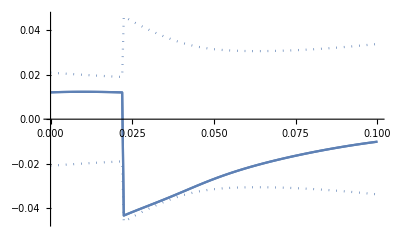

```mathematica
ReImPlot[Eigenvalues[jacobian][[{6,7}]]/.α->a/.pars/.(solut[a][[1]]),{a,0,.1},MaxRecursion->2]
```

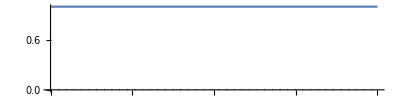

```mathematica
ReImPlot[1,{x,0,1},AspectRatio->1/4]
```

```mathematica
tab=Table[ReImPlot[i/.α->a/.pars/.(solut[a][[1]]),{a,.02,.025}],{i,Eigenvalues[jacobian]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

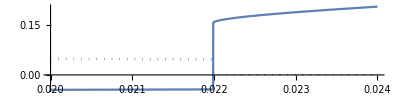
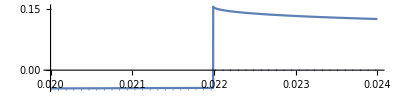
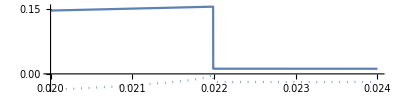
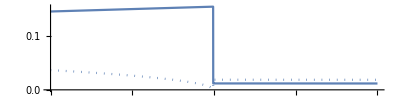

```mathematica
tab=Table[ReImPlot[i/.α->a/.pars/.(solut[a][[1]]),{a,.02,.024},AspectRatio->1/4],{i,Eigenvalues[jacobian][[{5,4,8,9}]]}]
```

```mathematica
Export["bifuracion.pdf",Show[tab,PlayRange->All]]
```

bifuracion.pdf

```mathematica
SystemOpen["bifuracion.pdf"]
```